# Simulating BZ Life Forms using a Phenomenological Model

#### Abhishek Sharma Cronin Lab University of Glasgow

```mathematica
baseDirectory=NotebookDirectory[]
```

C:\Users\abhishek\Desktop\BZ_GameOf_Life\

## BZ Life Form: Finite State Machine for Cell Stirrers

Finite State Logic for updating the PWM levels for the stirrers based on the observed states.
PWM 1: 0 (For random fluctuations)
PWM 2: 22 (For random fluctuations)
PWM 3: 50 (Center of the Life Form)
PWM 4: 30 (Neighbours of Life Form)

```mathematica
nCells=50; (* Number of cells along X and Y direction in the BZ Experiment *)
```

```mathematica
boundC[{x_,y_}]:={ Which[x==0,nCells,x==nCells+1,1,x>0&&x<nCells+1,x],Which[y== 0,nCells,y==nCells+1,1,y>0&&y<nCells+1,y]}
```

```mathematica
initCAState[nCells_,initLF_]:=Module[{CAState,initPos},CAState=ConstantArray[0,{nCells, nCells}];initPos=RandomInteger[{1,nCells},{2}]&/@Range[initLF];
Table[CAState⟦initPos⟦i,1⟧,initPos⟦i,2⟧⟧=1,{i,Length[initPos]}];
Return[CAState]]
```

```mathematica
initPWMState[CAState_,randomS_]:=Module[{PWMState,randomPos,nPos,lfPos},PWMState=ConstantArray[1,{nCells, nCells}];
randomPos=RandomInteger[{1,nCells},{2}]&/@Range[randomS];
Table[PWMState⟦randomPos⟦i,1⟧,randomPos⟦i,2⟧⟧=2,{i,Length[randomPos]}];
lfPos=Position[CAState,1];
nPos=Flatten[{{#⟦1⟧-1,#⟦2⟧},{#⟦1⟧+1,#⟦2⟧},{#⟦1⟧,#⟦2⟧-1},{#⟦1⟧,#⟦2⟧+1}}&/@lfPos,1];
nPos=boundC[#]&/@nPos;
Table[PWMState⟦nPos⟦i,1⟧,nPos⟦i,2⟧⟧=4,{i,Length[nPos]}];
Table[PWMState⟦lfPos⟦i,1⟧,lfPos⟦i,2⟧⟧=3,{i,Length[lfPos]}];
Return[PWMState]]
```

```mathematica
CAState=initCAState[nCells,50]; (* Initializing CA States *)
PWMState=initPWMState[CAState,100]; (* Initializing PWM States *)
```

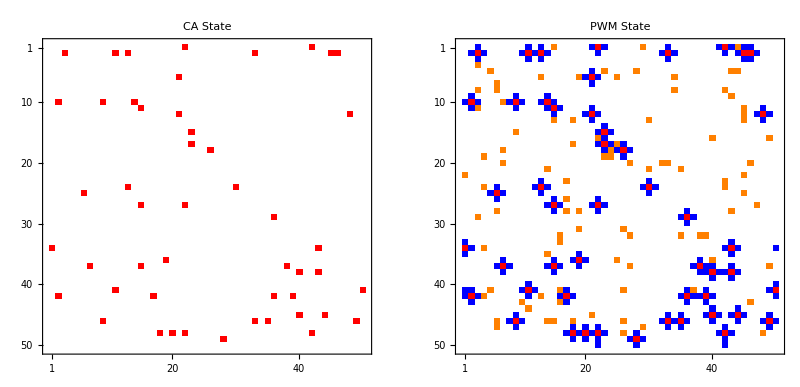

```mathematica
GraphicsRow[{MatrixPlot[CAState,PlotLabel-> "CA State",ImageSize->300,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},ColorRules->{0->White,1->Red}],MatrixPlot[PWMState,PlotLabel-> "PWM State",ImageSize->300,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},ColorRules->{1->White,2-> Orange,3-> Red,4->Blue}]}]
```

Game of Life State Machine : 

→ Get list of PWM states with value 3
→ Get list of nearest neighbours for the PWM states
→ Get list of next nearest neighbours for the PWM states

for cell in total cells:
→ if (cell PWM state == 3): 
    	→ nnLen = Count the list of nearest neighbours with CA state 1 
         → nnnLen = Count the list of next nearest neighbours with CA state 1
         → if (nnLen + nnnLen) == 1:
         		→ nCell : cell with CA state == 1
         	→ else if  (nnLen + nnnLen) > 1:
           	→ nCell : randomly selected cell among the neighbouring cells with CA state == 1
         
          → if (nCell is nearest neighbour)
         		→ if nCell PWM state == 3:
         			→ Randomly select the cell state between PWM states 1/3
         			→ Other cell PWM state = 4
         		→ else:
         			→ Propagation Event : nCell PWM state = 3 and Cell PWM state = 4 
	→ if nCell is next nearest neighbour
         			→ Replication Event : nCell PWM state = 3 and cell PWM state = 1

→ Update PWM states to 4 near the PWM 3 levels from available locations
→ Update PWM states to 2 based on random selection from available locations

```mathematica
boundC[x_,y_]:={ Which[x==0,nCells,x==nCells+1,1,x>0&&x<nCells+1,x],Which[y== 0,nCells,y==nCells+1,1,y>0&&y<nCells+1,y]}
```

```mathematica
bzlifeFSM[CAState_,PWMState_,randomS_]:=Module[{nPWMState,chMat,lfPos,nnList,nnnList,rand,nList,nnCAList,nnPWMList,nnnCAList,nnCells,nnnCells,sCell,cnt=0},
nPWMState=ConstantArray[1,Dimensions[PWMState]];
chMat= ConstantArray[0,Dimensions[PWMState]]; (* Array to track if changes are possible *)
lfPos=Position[PWMState,3];
(nPWMState⟦#⟦1⟧,#⟦2⟧⟧=3)&/@lfPos;
nnList={{#⟦1⟧-1,#⟦2⟧},{#⟦1⟧+1,#⟦2⟧},{#⟦1⟧,#⟦2⟧-1},{#⟦1⟧,#⟦2⟧+1}}&/@lfPos;
nnnList={{#⟦1⟧+1,#⟦2⟧+1},{#⟦1⟧+1,#⟦2⟧-1},{#⟦1⟧-1,#⟦2⟧+1},{#⟦1⟧-1,#⟦2⟧-1}}&/@lfPos;
nnList=Apply[boundC,nnList,{2}];
nnnList=Apply[boundC,nnnList,{2}];
nnCAList=Table[CAState⟦#⟦1⟧,#⟦2⟧⟧&/@nnList⟦i⟧,{i,Length[lfPos]}];
nnPWMList=Table[PWMState⟦#⟦1⟧,#⟦2⟧⟧&/@nnList⟦i⟧,{i,Length[lfPos]}];
nnnCAList=Table[CAState⟦#⟦1⟧,#⟦2⟧⟧&/@nnnList⟦i⟧,{i,Length[lfPos]}];
nnCells=Block[{caPos},caPos=Flatten[Position[nnCAList⟦#⟧,1]]
&/@Range[Length[lfPos]];
Which[Length[caPos⟦#⟧]== 0,{},Length[caPos⟦#⟧]==1,caPos⟦#⟧,Length[caPos⟦#⟧]>1,rand=RandomInteger[{1,Length[caPos⟦#⟧]}];{caPos⟦#,rand⟧}]&/@Range[Length[lfPos]]];

nnnCells=Block[{caPos},caPos=Flatten[Position[nnnCAList⟦#⟧,1]]
&/@Range[Length[lfPos]]; 
Which[Length[caPos⟦#⟧]== 0,{},Length[caPos⟦#⟧]==1,caPos⟦#⟧,Length[caPos⟦#⟧]>1,rand=RandomInteger[{1,Length[caPos⟦#⟧]}];{caPos⟦#,rand⟧}]&/@Range[Length[lfPos]]];

sCell=Which[
Length[nnCells⟦#⟧]==0&&Length[nnnCells⟦#⟧]==1,{2,#,nnnCells⟦#⟧,lfPos⟦#⟧,First@nnnList⟦#,nnnCells⟦#⟧⟧},
Length[nnCells⟦#⟧]==1&&Length[nnnCells⟦#⟧]==0,{1,#,nnCells⟦#⟧,lfPos⟦#⟧,First@nnList⟦#,nnCells⟦#⟧⟧},
Length[nnCells⟦#⟧]==1&&Length[nnnCells⟦#⟧]==1,If[RandomInteger[]==1,{1,#,nnCells⟦#⟧,lfPos⟦#⟧,First@nnList⟦#,nnCells⟦#⟧⟧},{2,#,nnnCells⟦#⟧,lfPos⟦#⟧,First@nnnList⟦#,nnnCells⟦#⟧⟧}]]&/@Range[Length[lfPos]]/.Null->Sequence[];

(* Propagation and Replication Events *)
If[#⟦1⟧==1,
If[PWMState⟦#⟦5,1⟧,#⟦5,2⟧⟧==3,
If[RandomInteger[]==0,
nPWMState⟦#⟦4,1⟧,#⟦4,2⟧⟧=3,nPWMState⟦#⟦4,1⟧,#⟦4,2⟧⟧=1],
nPWMState⟦#⟦4,1⟧,#⟦4,2⟧⟧=1;nPWMState⟦#⟦5,1⟧,#⟦5,2⟧⟧=3;
chMat⟦#⟦4,1⟧,#⟦4,2⟧⟧=1]]&/@sCell; 
If[#⟦1⟧==2,nPWMState⟦#⟦5,1⟧,#⟦5,2⟧⟧=3]&/@sCell;
(chMat⟦#⟦1⟧,#⟦2⟧⟧=1)&/@Evaluate[Position[nPWMState,3]];

lfPos=Position[nPWMState,3];
nnList={{#⟦1⟧-1,#⟦2⟧},{#⟦1⟧+1,#⟦2⟧},{#⟦1⟧,#⟦2⟧-1},{#⟦1⟧,#⟦2⟧+1}}&/@lfPos;
nnList=Flatten[Apply[boundC,nnList,{2}],1];
If[chMat⟦#⟦1⟧,#⟦2⟧⟧≠1,nPWMState⟦#⟦1⟧,#⟦2⟧⟧=4]&/@nnList;
(chMat⟦#⟦1⟧,#⟦2⟧⟧=1)&/@nnList;

Block[{pos},While[cnt≠randomS,pos=RandomInteger[{1,nCells},{2}];If[chMat⟦pos⟦1⟧,pos⟦2⟧⟧≠1,nPWMState⟦pos⟦1⟧,pos⟦2⟧⟧=2;chMat⟦pos⟦1⟧,pos⟦2⟧⟧=1;cnt=cnt+1];]];
Return[nPWMState]]
```

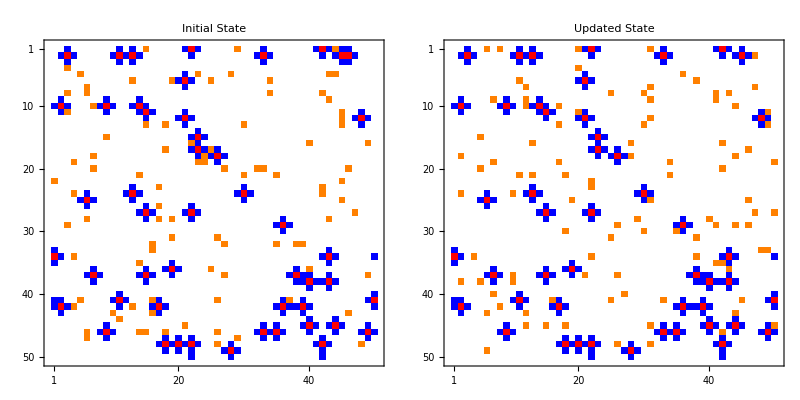

```mathematica
GraphicsRow[{MatrixPlot[PWMState,PlotLabel-> "Initial State",ImageSize->300,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},ColorRules->{1->White,2-> Orange,3-> Red,4->Blue}],MatrixPlot[bzlifeFSM[CAState,PWMState,100],PlotLabel-> "Updated State",ImageSize->300,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},ColorRules->{1->White,2-> Orange,3-> Red,4->Blue}]},Spacings->0]
```

## Testing Game of Life : Finite State Machine

```mathematica
nCells=5;
basicPWM=ConstantArray[1,{nCells,nCells}];
basicPWM⟦3,3⟧=3;basicPWM⟦2,3⟧=4;basicPWM⟦4,3⟧=4;basicPWM⟦3,2⟧=4;basicPWM⟦3,4⟧=4;
```

```mathematica
p0=MatrixPlot[basicPWM,ImageSize->120,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->16]},ColorRules->{1->White,2-> Orange,3-> Red,4->Blue}]
```

-Graphics-

#### Testing Propagation:

```mathematica
basicCA=ConstantArray[0,{5,5}];
basicCA⟦3,3⟧=1;basicCA⟦3,4⟧=1;
```

```mathematica
p1=GraphicsRow[{MatrixPlot[basicCA,ImageSize->100,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->16]},ColorRules->{0->White,1->Red}],MatrixPlot[bzlifeFSM[basicCA,basicPWM,2],ImageSize->100,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->16]},ColorRules->{1->White,2-> Orange,3-> Red,4->Blue}]},Spacings->0,ImageSize->300]
```

-Graphics-

#### Testing Replication:

```mathematica
basicCA=ConstantArray[0,{5,5}];
basicCA⟦3,3⟧=1;basicCA⟦4,4⟧=1;
```

```mathematica
p2=GraphicsRow[{MatrixPlot[basicCA,ImageSize->100,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->16]},ColorRules->{0->White,1->Red}],MatrixPlot[bzlifeFSM[basicCA,basicPWM,2],ImageSize->100,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->16]},ColorRules->{1->White,2-> Orange,3-> Red,4->Blue}]},Spacings->0,ImageSize->300]
```

-Graphics-

#### Testing Multiple Events

```mathematica
basicCA=ConstantArray[0,{5,5}];
basicCA⟦3,3⟧=1;basicCA⟦3,4⟧=1;basicCA⟦4,3⟧=1;
```

```mathematica
p3=GraphicsRow[{MatrixPlot[basicCA,ImageSize->100,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->16]},ColorRules->{0->White,1->Red}],MatrixPlot[bzlifeFSM[basicCA,basicPWM,2],ImageSize->100,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->16]},ColorRules->{1->White,2-> Orange,3-> Red,4->Blue}]},Spacings->0,ImageSize->300]
```

-Graphics-

```mathematica
basicCA=ConstantArray[0,{5,5}];
basicCA⟦3,3⟧=1;basicCA⟦4,4⟧=1;basicCA⟦2,2⟧=1;
```

```mathematica
p4=GraphicsRow[{MatrixPlot[basicCA,ImageSize->100,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->16]},ColorRules->{0->White,1->Red}],MatrixPlot[bzlifeFSM[basicCA,basicPWM,2],ImageSize->100,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->16]},ColorRules->{1->White,2-> Orange,3-> Red,4->Blue}]},Spacings->0,ImageSize->300]
```

-Graphics-

```mathematica
basicCA=ConstantArray[0,{5,5}];
basicCA⟦3,3⟧=1;basicCA⟦4,4⟧=1;basicCA⟦2,2⟧=1;basicCA⟦3,4⟧=1;basicCA⟦4,3⟧=1;
```

```mathematica
p5=GraphicsRow[{MatrixPlot[basicCA,ImageSize->100,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->16]},ColorRules->{0->White,1->Red}],MatrixPlot[bzlifeFSM[basicCA,basicPWM,2],ImageSize->100,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->16]},ColorRules->{1->White,2-> Orange,3-> Red,4->Blue}]},Spacings->0,ImageSize->300]
```

-Graphics-

#### Testing Competition

```mathematica
nCells=5;
basicPWM=ConstantArray[1,{nCells,nCells}];
basicPWM⟦3,3⟧=3;
basicPWM⟦2,3⟧=3;
basicPWM⟦4,3⟧=4;
basicPWM⟦3,2⟧=4;
basicPWM⟦3,4⟧=4;
basicPWM⟦2,2⟧=4;basicPWM⟦2,4⟧=4;basicPWM⟦1,3⟧=4;
```

```mathematica
p6=MatrixPlot[basicPWM,ImageSize->120,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->16]},ColorRules->{1->White,2-> Orange,3-> Red,4->Blue}]
```

-Graphics-

```mathematica
basicCA=ConstantArray[0,{5,5}];
basicCA⟦3,3⟧=1;basicCA⟦2,3⟧=1;
```

```mathematica
p7=GraphicsRow[{MatrixPlot[basicCA,ImageSize->100,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->16]},ColorRules->{0->White,1->Red}],MatrixPlot[bzlifeFSM[basicCA,basicPWM,2],ImageSize->100,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->16]},ColorRules->{1->White,2-> Orange,3-> Red,4->Blue}]},Spacings->0,ImageSize->300]
```

-Graphics-

```mathematica
basicCA=ConstantArray[0,{5,5}];
basicCA⟦3,3⟧=1;basicCA⟦2,3⟧=1;
```

```mathematica
p8=GraphicsRow[{MatrixPlot[basicCA,ImageSize->100,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->16]},ColorRules->{0->White,1->Red}],MatrixPlot[bzlifeFSM[basicCA,basicPWM,2],ImageSize->100,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->16]},ColorRules->{1->White,2-> Orange,3-> Red,4->Blue}]},Spacings->0,ImageSize->300]
```

-Graphics-

```mathematica
basicCA=ConstantArray[0,{5,5}];
basicCA⟦3,3⟧=1;basicCA⟦2,3⟧=1;
```

```mathematica
p9=GraphicsRow[{MatrixPlot[basicCA,ImageSize->100,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->16]},ColorRules->{0->White,1->Red}],MatrixPlot[bzlifeFSM[basicCA,basicPWM,2],ImageSize->100,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->16]},ColorRules->{1->White,2-> Orange,3-> Red,4->Blue}]},Spacings->0,ImageSize->300]
```

-Graphics-

```mathematica
Export[baseDirectory<>"p0.svg",p0]
```

C:\Users\abhishek\Desktop\BZ_GameOf_Life\p0.svg

```mathematica
Export[baseDirectory<>"p1.svg",p1]
```

C:\Users\abhishek\Desktop\BZ_GameOf_Life\p1.svg

```mathematica
Export[baseDirectory<>"p2.svg",p2]
```

C:\Users\abhishek\Desktop\BZ_GameOf_Life\p2.svg

```mathematica
Export[baseDirectory<>"p3.svg",p3]
```

C:\Users\abhishek\Desktop\BZ_GameOf_Life\p3.svg

```mathematica
Export[baseDirectory<>"p4.svg",p4]
```

C:\Users\abhishek\Desktop\BZ_GameOf_Life\p4.svg

```mathematica
Export[baseDirectory<>"p5.svg",p5]
```

C:\Users\abhishek\Desktop\BZ_GameOf_Life\p5.svg

```mathematica
Export[baseDirectory<>"p6.svg",p6]
```

C:\Users\abhishek\Desktop\BZ_GameOf_Life\p6.svg

```mathematica
Export[baseDirectory<>"p7.svg",p7]
```

C:\Users\abhishek\Desktop\BZ_GameOf_Life\p7.svg

```mathematica
Export[baseDirectory<>"p8.svg",p8]
```

C:\Users\abhishek\Desktop\BZ_GameOf_Life\p8.svg

```mathematica
Export[baseDirectory<>"p9.svg",p9]
```

C:\Users\abhishek\Desktop\BZ_GameOf_Life\p9.svg

## BZ Life Form: Phenomenological Model for updating CA states

In this section, we develop the phenomenological model for updating the CA states based on the current CA state of cell and its neighbours and applied PWM Levels. 

CA_state^(t+1)= f(CA_state^t, PWM_state^t)

Due to complex hydrodynamic coupling between the cells, we define probabilities of updating states based on the given set of PWM levels and CA states. Here we write down the list of probabilities for different possible combinations : 
Cell State 0 : Light Blue (Weak Oscillations)
Cell State 1 : Dark Blue (Strong Oscillations)
To update CA states, we will iterate through all the cells and update the states based on PWM level of cell and nearest neighbours.

```mathematica
nCells=50;
```

```mathematica
facCellType=0.7;
```

```mathematica
prob1=0.50;(* When nCells with PWM(3)≥3 *)
```

```mathematica
prob2=0.30;(* When nCells with PWM(3)<3 *)
```

```mathematica
prob3=0.25;(* When nCells with PWM(3)==0 and When nCells with PWM(4)≥3 *)
```

```mathematica
prob4=0.15;(* When nCells with PWM(3)==0 and When nCells with PWM(4)<3 *)
```

```mathematica
fac1=0.0; (* When Cell PWM is 1 *)
```

```mathematica
fac2=0.1 ;(* When Cell PWM is 2 *)
```

```mathematica
fac3=0.5;(* When Cell PWM is 4 *)
```

```mathematica
probHigh=0.5;(* When Cell PWM is 3 *)
```

```mathematica
boundC[x_,y_]:={ Which[x==0,nCells,x==nCells+1,1,x>0&&x<nCells+1,x],Which[y== 0,nCells,y==nCells+1,1,y>0&&y<nCells+1,y]}
```

```mathematica
updateCellState[{i_,j_},{CAState_,PWMState_}]:=Block[{cellCA=CAState⟦i,j⟧,cellPWM=PWMState⟦i,j⟧,nList,nPWM,nPWM3,nPWM4,prob},nList={{i-1,j},{i+1,j},{i,j-1},{i,j+1}};
nList=Flatten[Apply[boundC,{nList},{2}],1];(* Getting neighbour lists *)
nPWM=PWMState⟦#⟦1⟧,#⟦2⟧⟧&/@nList;(* Getting neighbour PWM levels *)
nPWM3=Length@Position[nPWM,3];(* Getting number of neighbours with PWM levels 3 *)
nPWM4=Length@Position[nPWM,4];(* Getting number of neighbours with PWM levels 4 *)
prob=Which[nPWM3≥3,prob1,nPWM3<3 && nPWM3≥1,prob2,nPWM3==0 && nPWM4≥3 ,prob3,nPWM3==0 && nPWM4<3&& nPWM4≥1,prob4,nPWM3==0 && nPWM4==0,0];
Return[Block[{prob1},Which[cellCA== 0,
prob1=facCellType Which[cellPWM==1,prob fac1,cellPWM==2,prob fac2,cellPWM==3,probHigh,cellPWM==4,prob fac3];
RandomChoice[{prob1,1-prob1}->{1,0}],
cellCA==1,
prob1=Which[cellPWM==1,prob fac1,cellPWM==2,prob fac2,cellPWM==3,probHigh,cellPWM==4,prob fac3];
RandomChoice[{prob1,1-prob1}->{1,0}]
]]]]
```

```mathematica
CAState=initCAState[nCells,100]; (* Initializing CA States *)
PWMState=initPWMState[CAState,100]; (* Initializing PWM States *)
CAStateN=Table[updateCellState[{i,j},{CAState,PWMState}],{i,nCells},{j,nCells}];
```

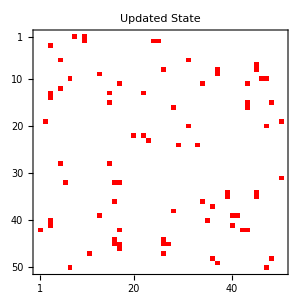

```mathematica
MatrixPlot[CAStateN,PlotLabel-> "Updated State",ImageSize->300,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},ColorRules->{0->White,1-> Red}]
```

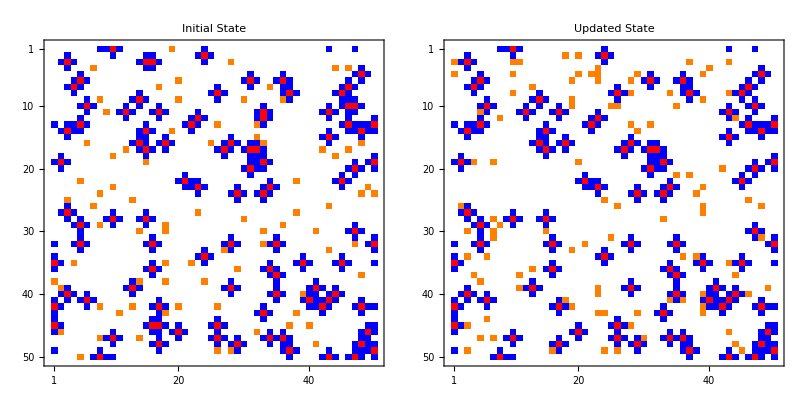

```mathematica
GraphicsRow[{MatrixPlot[PWMState,PlotLabel-> "Initial State",ImageSize->300,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},ColorRules->{1->White,2-> Orange,3-> Red,4->Blue}],MatrixPlot[bzlifeFSM[CAState,PWMState,100],PlotLabel-> "Updated State",ImageSize->300,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},ColorRules->{1->White,2-> Orange,3-> Red,4->Blue}]},Spacings->0]
```

## Testing BZ Life Forms Simulation

```mathematica
nCells=50;nSteps=5000; initLifeForms=10;numRandom=500;
```

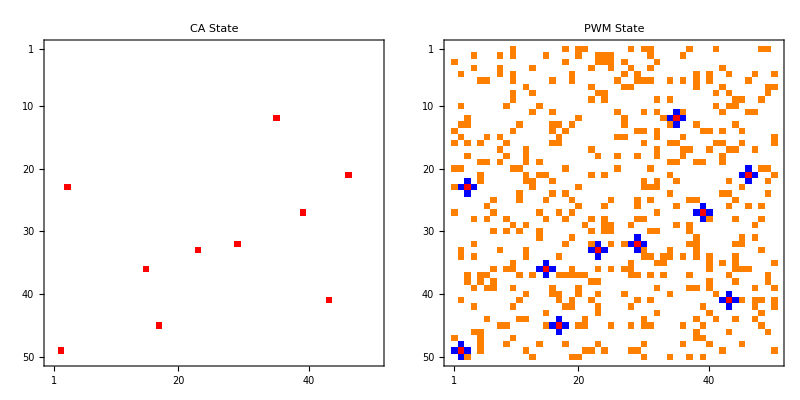

```mathematica
CAState=initCAState[nCells,initLifeForms]; (* Initializing CA States *)
PWMState=initPWMState[CAState,numRandom]; (* Initializing PWM States *)
GraphicsRow[{MatrixPlot[CAState,PlotLabel-> "CA State",ImageSize->300,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},ColorRules->{0->White,1->Red}],MatrixPlot[PWMState,PlotLabel-> "PWM State",ImageSize->300,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},ColorRules->{1->White,2-> Orange,3-> Red,4->Blue}]},Spacings->0]
```

```mathematica
allPWMStates={};allCAStates={};(* Empty matrices to store PWM and CA states *)
```

```mathematica
cnt=0;Monitor[While[cnt≤ nSteps,
PWMState=bzlifeFSM[CAState,PWMState,numRandom];
CAState=Table[updateCellState[{i,j},{CAState,PWMState}],{i,nCells},{j,nCells}];
allPWMStates=Join[allPWMStates,{PWMState}];
allCAStates=Join[allCAStates,{CAState}];
cnt=cnt+1],cnt]
```

```mathematica
Dimensions/@{allPWMStates,allCAStates}
```

{{5001,50,50},{5001,50,50}}

```mathematica
Export[baseDirectory<>"\\PWM_data.mx",allPWMStates];
Export[baseDirectory<>"\\CA_data.mx",allCAStates];
```

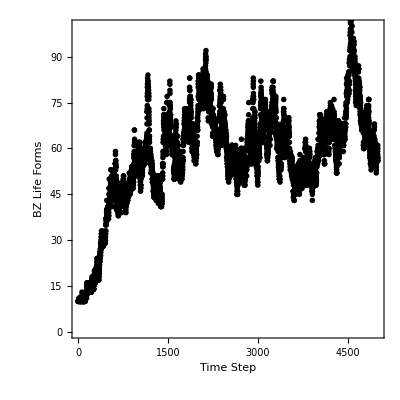

```mathematica
ListPlot[Length[Position[allPWMStates⟦#⟧,3]]&/@Range[nSteps],PlotStyle->{Black,PointSize[0.01]},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotRange->{0,100},Frame-> True,AspectRatio->1,FrameLabel->{"Time Step","BZ Life Forms"},ImageSize->400]
```

Creating Images for each time step (a directory Images should exist)

```mathematica
baseDirectory
```

C:\Users\abhishek\Desktop\BZ_GameOf_Life\

```mathematica
ParallelTable[Block[{plot},plot=GraphicsRow[{MatrixPlot[allCAStates⟦i⟧,PlotLabel-> "CA State: Time Step "<>ToString[i],ImageSize->300,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},ColorRules->{0->White,1-> Red}],MatrixPlot[allPWMStates⟦i⟧,PlotLabel-> "PWM State State: Time Step "<>ToString[i],ImageSize->300,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},ColorRules->{1->White,2-> Orange,3-> Red,4->Blue}]},Spacings->0,ImageSize->1000];
Export[baseDirectory<>"\\Images\\Image"<>ToString[i]<>".png",plot]],{i,nSteps}];
```